```mathematica
Quit[]
```

## Create test figure

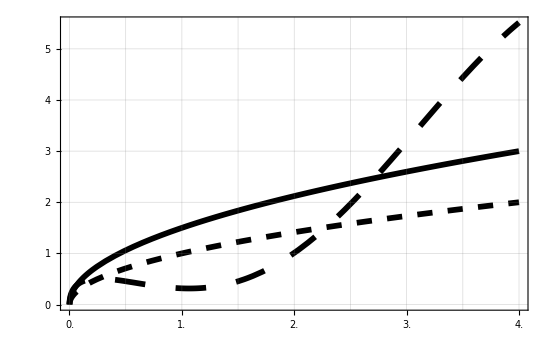

```mathematica
testFig=Plot[{√x,2 √x-2Sin[x],3/2 x^(1/2)},{x,0,4},PlotStyle->{Directive[Dashing[0.02],Black,Thickness[0.0075]],Directive[Dashing[0.04],Black,Thickness[0.0075]],Directive[Black,Thickness[0.0075]]},Frame->True,GridLines->{Range[0,4,0.5],Range[0,5]},GridLinesStyle->Directive[Thick,Opacity[0.3], Gray],FrameTicks->{{Range[0,6,1],None},{Range[0,4,0.5],None}},FrameTicksStyle->Directive[Black,14],ImageSize->550]
```

### Export to pdf file

```mathematica
Export["testFig.pdf",testFig,ImageResolution->720]
```

testFig.pdf

### Snapshot take from pdf, range: 0≤x≤4 and 0≤y≤5 (it’s better to snapshot from the axes origin to some place with a definite tick)

```mathematica
testFig1=-Graphics-;
```

## Extract the points

```mathematica
<<PointExtract`
```

### Press mouse (prime button) on the figure while holding Shift Key to create a region (the mouse pressing as vertices and their connection as boundary of the polygon-like region) , in which the curves are about to be extracted. The solid line shows the region boundary already selected, the dashed line indicates the boundary waiting to be confirmed by mouse press. Release the Shift Key to end the selection Release the Shift Key and press hold again to clear the region and start new region.

```mathematica
RgnSlct["testFig1","coords1"]
```

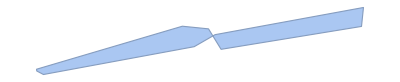

```mathematica
Rgn=BoundaryDiscretizeRegion[Polygon[coords1]]
```

### Take mean value of points with the same x-value (due to the width of curves) and rescale the points to data set

```mathematica
PntsExtrctd=DataExtrct["testFig1",coords1,({4#⟦1⟧,5#⟦2⟧}/ImageDimensions[testFig1])&];
```

## Compare extraction and original curve

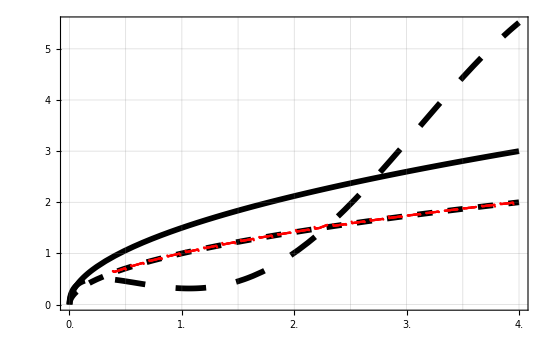

```mathematica
Show[{testFig,ListPlot[PntsExtrctd,PlotStyle->{Red,PointSize[0.003]}]}]
```

## example: LogPlot

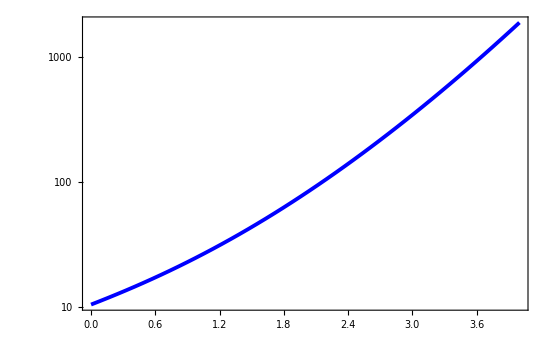

```mathematica
LogPlotTest=LogPlot[Exp[(1/3 x+√2)^2]+x+3,{x,0,4},PlotStyle->{Blue,Thickness[0.005]},Frame->True,GridLines->{Range[0,4,1],Automatic},GridLinesStyle->Directive[Gray,Opacity[0.5], Thick],AxesOrigin->{0,0},ImageSize->550,FrameTicksStyle->Directive[Black,14]]
```

```mathematica
Export["LogPlotTest.pdf",LogPlotTest]
```

LogPlotTest.pdf

```mathematica
SystemOpen["LogPlotTest.pdf"]
```

```mathematica
LogTest=-Graphics-;
```

```mathematica
RgnSlct["LogTest","coords"]
```

```mathematica
ImageDimensions[LogTest]
```

{753,386}

```mathematica
rawdata=DataExtrct["LogTest",coords,Identity];
```

log[y] in LogPlot are linear mapped to pixel coordinates

```mathematica
Assuming[yx>0&&Logy>0,Solve[(Log[yx]-Log[10])/Logy==(Log[1000]-Log[10])/386,yx]//Simplify]
```

{{yx→10^(Logy/193+1)}}

```mathematica
dat={4(#⟦1⟧)/753,10^(1+(#⟦2⟧)/193)}&/@rawdata;
```

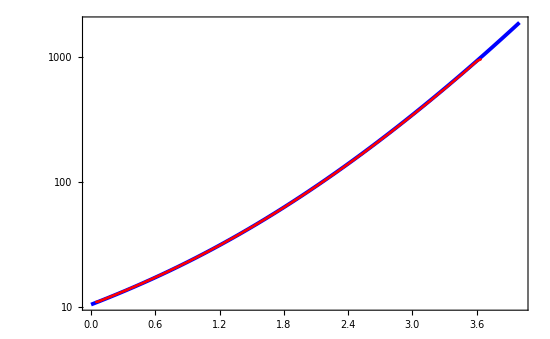

```mathematica
Show[{LogPlotTest,ListLogPlot[dat,PlotStyle->{Red,PointSize[0.003]}]}]
```

For more general case, Logy1 is the is the the pixel coordinate of a point (x1,y1=f(x)), Logy0 is the pixel coordinate of origin, y ,dmsny=ImageDimensions[“pic”]⟦2⟧.

```mathematica
Assuming[yx>0&&y0>0&&y1>0&&Logy1∈Reals&&Logy0∈Reals&&dmsny>0,Solve[(Log[yx]-Log[y0])/(Logy1-Logy0)==(Log[y1]-Log[y0])/dmsny,yx]//FullSimplify]⟦1⟧
```

{yx→y0^((dmsny+Logy0-Logy1)/dmsny) y1^((Logy1-Logy0)/dmsny)}